## Introduction

This code explores epidemiological models of wild felines (ocelots) and domestic dogs, sharing a parasite transmitted environmentally. We have parameterized the model . The results of this model are soon to be published in Ecosphere (Vargas Soto et al. 2024).

### Model Structure

In our model, there are two separate pools of infectious stages, one mostly associated with the natural environments and one more associated with human-modified habitats. This model lets us explore the parameter space of proportion of scat shed in each pool. The model is represented by the following system of ODEs:

dS_D/dt=ρ_D I_D-ω_D β_H κ_D L_H S_D-(1-ω_D)β_N κ_D L_N S_D
dI_D/dt=-ρ_D I_D+ω_D β_H κ_D L_H S_D+(1-ω_D)β_N κ_D L_N S_D
dE_H/dt=ω_W λ_W I_W+ω_D λ_D I_D-μ_E E_H-δ E_H-
dE_N/dt=(1-ω_W)λ_W I_W+(1-ω_D)λ_D I_D-μ_E E_2-δ E_2
dL_H/dt=δ E_H-μ_L L_H-β_H L_H ω_D(S_D+I_D)-β_H L_H ω_W(S_W+I_W)
dL_N/dt=δ E_N-μ_L L_N-β_N L_N(1-ω_D)(S_D+I_D)-β_N L_N(1-ω_W)(S_W+I_W)
dS_W/dt=ρ I_W-ω_W β_H L_H κ_W S_W-(1-ω_W)β_N L_N κ_W S_W
dI_W/dt=-ρ I_W+ω_W β_H L_H κ_W S_W+(1-ω_W)β_N L_N κ_W S_W

The shedding rates λ and the infection rates β are scaled by coefficient of overlap ω that represent the proportion of interactions with scat that occur in each habitat type. Thus, the proportion of scat that dogs deposited and interact with in their own pool is high, while the proportion for wild hosts in the human-modified pool is low.

### Parameter estimates

Adult worms survive for up to six weeks in their hosts, so we estimate the rate of host recovery ρ=0.024 days-1 (Komiya et al. 1956). 
Eggs develop into larvae at a rate of 0.044/day (Foster and Daengsvang 1932). 
Scat loses infecting ability as the number of live larvae in it die. We use the mean survival duration of larvae, and obtain μ_L=0.152/day. Similarly, egg mortality is estimated μ_E=0.069/day. 
The probability of infection given contact is very high for dogs and A. caninum, around 0.97. In contrast, the probability is <1/12 (combined oral and dermal exposure) for cats exposed to this dog parasite. We scale these values by 50% and obtain κ_D=0.97 2=0.485 and κ_W=0.042. The estimated proportion σ of compatibility is thus κ_W/κ_D=0.083/0.97=0.086.
The cat defecation rate was taken from a study of leopards, and is estimated at λ_W=1.667/day.
In a study of rural dogs in cacao plantations, 10 dogs were observed for six days each, and 87 defecation events were observed (dos Santos et al. 2018. J. Mamm. 99:1261). The estimate defecation rate is then λ_D=82/(10 6)=1.37. 
FInally, the coefficient of overlap was estimated as ω=0.358 based on camera-trap surveys. This estimate was based on frequencies of use of trails of 0.024/day for ocelots, and 0.067/day for dogs. These were likely overestimates. I have corrected the calculation, and obtained frequencies of 0.087/day for dogs, and 0.22 for ocelots. I use the value for ocelots as the x value in the contour plots. This assumes that about 1/5 of ocelot interactions with scat, be it depositing or picking up, will occur on “domestic” habitats. This is likely higher than the true value.

### Estimation of β

We estimate β as the value that would produce the closest value to the observed prevalence in dogs (74%) without the contribution of wild hosts. For this we set ω_W=0, and ω_D=1, meaning dogs don’t ever go into natural habitats, and cats never go into human habitats.

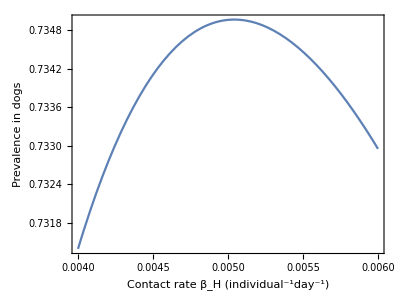

```mathematica
ndsolb[βn_,βh_]:= With[{κd=0.97/2,κw=1/12/2,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.082,μe=0.069,
ρ=1/42,
ωd=1,ωw=0},NDSolve[
{Sd'[t]==-ωd κd βh Sd[t] Lh[t]-(1-ωd)κd βn Sd[t] Ln[t]+ρ Id[t],
Id'[t]==ωd κd βh Sd[t] Lh[t]+(1-ωd)κd βn Sd[t] Ln[t]-ρ Id[t],
Eh'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe Eh[t]-δ Eh[t]-βh  Eh[t](ωd(Sd[t]+Id[t])+ ωw(Sw[t]+Iw[t])),
En'[t]==(1-ωw) λw Iw[t]+ (1-ωd)λd Id[t]-μe En[t]-δ En[t]-βn  En[t]((1-ωd)(Sd[t]+Id[t])+(1- ωw)(Sw[t]+Iw[t])),
Lh'[t]==δ Eh[t]-μl Lh[t]-ωd βh  Lh[t](Sd[t]+Id[t])-ωw βh  Lh[t](Sw[t]+Iw[t]),
Ln'[t]==δ En[t]-μl Ln[t]- (1-ωd)βn Ln[t](Sd[t]+Id[t])-(1-ωw)βn  Ln[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw   κw βh Sw[t]Lh[t]-(1-ωw)   κw βn Sw[t]Ln[t]+ρ Iw[t],
Iw'[t]==ωw   κw βh Sw[t]Lh[t]+(1-ωw)   κw βn Sw[t]Ln[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, Lh[0]==0,Ln[0]==0,Eh[0]==0,En[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,Lh,Ln,Eh,En,Sd,Sw},
{t,0,700}]];
With[{finalt = 700},
Plot[Id[finalt]/(Id[finalt]+Sd[finalt])/.ndsolb[1,βh],{βh,0.004,0.006}, Frame->True, FrameLabel->{"Contact rate β_H (individual^-1day^-1)", "Prevalence in dogs"}, LabelStyle->18, AspectRatio->3/4]]
```

With the two-pool model, the β parameter estimate that would produce the maximum prevalence in dogs (74%) is β=0.0050.

#### Scenario 1: Parasite of dogs

One potential scenario is that cats acquire a parasite of dogs, like Ancylostoma caninum. This parasite would have high probability of infection in their natural host, and much lower in cats. We estimate κ_D=0.97/2 and κ_W=0.083/2.

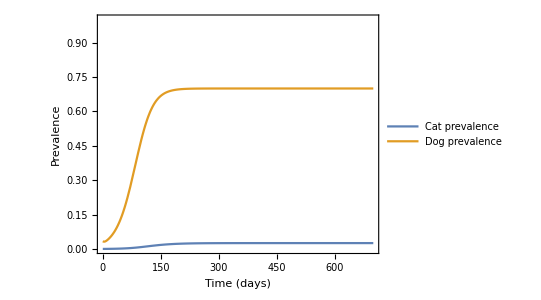

```mathematica
With[{κd=0.97/2,κw = 1/12/2,
λw=0,λd=82/60,
μl=1/6.6,δ=0.082,μe=0.069,
ρ=1/42,
ωw=0.13,ωd=1,
βh=0.005, βn=0.005/2},
Plot[Evaluate[{Iw[t]/(Iw[t]+Sw[t]),Id[t]/(Id[t]+Sd[t])}/.
NDSolve[
{Sd'[t]==-ωd κd βh Sd[t] Lh[t]-(1-ωd)κd βn Sd[t] Ln[t]+ρ Id[t],
Id'[t]==ωd κd βh Sd[t] Lh[t]+(1-ωd)κd βn Sd[t] Ln[t]-ρ Id[t],
Eh'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe Eh[t]-δ Eh[t]-βh  Eh[t](ωd(Sd[t]+Id[t])+ ωw(Sw[t]+Iw[t])),
En'[t]==(1-ωw) λw Iw[t]+ (1-ωd)λd Id[t]-μe En[t]-δ En[t]-βn  En[t]((1-ωd)(Sd[t]+Id[t])+(1- ωw)(Sw[t]+Iw[t])),
Lh'[t]==δ Eh[t]-μl Lh[t]-ωd βh  Lh[t](Sd[t]+Id[t])-ωw βh  Lh[t](Sw[t]+Iw[t]),
Ln'[t]==δ En[t]-μl Ln[t]- (1-ωd)βn Ln[t](Sd[t]+Id[t])-(1-ωw)βn  Ln[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw   κw βh Sw[t]Lh[t]-(1-ωw)   κw βn Sw[t]Ln[t]+ρ Iw[t],
Iw'[t]==ωw   κw βh Sw[t]Lh[t]+(1-ωw)   κw βn Sw[t]Ln[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, Lh[0]==0,Ln[0]==0,Eh[0]==0,En[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,Lh,Ln,Eh,En,Sd,Sw},
{t,0,700}]],
{t,0,700},
PlotLegends->{"Cat prevalence","Dog prevalence"},
LabelStyle->"Subsubtitle",
Frame->True,
FrameLabel->{"Time (days)","Prevalence"},
(*LabelStyle->Large,ImageSize->Large,*)
PlotRange->{Automatic,{0,1}},
PlotStyle->Thick, AspectRatio->3/4]]
```

#### Different degrees of overlap

The contour plot explores how the expected prevalence in wild hosts at equilibrium changes with respect to changes in parameter values. We explore how higher overlap would change the expected prevalence, by modifying the ω parameters. The ω_i parameter represents the proportion of scat that  host species i interacts with in the “domestic” pool (Pool 1), and (1-ω) represents the proportion in the “wild” pool.

```mathematica
ndsol = With[{κd=0.97/2,κw = 1/12/2,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.082,μe=0.069,
ρ=1/42,
(*ωw=0.358,ωd=1,*)
βh=0.005, βn=0.005/2},NDSolve[
{Sd'[t]==-ωd κd βh Sd[t] Lh[t]-(1-ωd)κd βn Sd[t] Ln[t]+ρ Id[t],
Id'[t]==ωd κd βh Sd[t] Lh[t]+(1-ωd)κd βn Sd[t] Ln[t]-ρ Id[t],
Eh'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe Eh[t]-δ Eh[t]-βh  Eh[t](ωd(Sd[t]+Id[t])+ ωw(Sw[t]+Iw[t])),
En'[t]==(1-ωw) λw Iw[t]+ (1-ωd)λd Id[t]-μe En[t]-δ En[t]-βn  En[t]((1-ωd)(Sd[t]+Id[t])+(1- ωw)(Sw[t]+Iw[t])),
Lh'[t]==δ Eh[t]-μl Lh[t]-ωd βh  Lh[t](Sd[t]+Id[t])-ωw βh  Lh[t](Sw[t]+Iw[t]),
Ln'[t]==δ En[t]-μl Ln[t]- (1-ωd)βn Ln[t](Sd[t]+Id[t])-(1-ωw)βn  Ln[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw   κw βh Sw[t]Lh[t]-(1-ωw)   κw βn Sw[t]Ln[t]+ρ Iw[t],
Iw'[t]==ωw   κw βh Sw[t]Lh[t]+(1-ωw)   κw βn Sw[t]Ln[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, Lh[0]==0,Ln[0]==0,Eh[0]==0,En[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,Lh,Ln,Eh,En,Sd,Sw},
{t,0,700}]];
With[{finalt = 700},
Show[
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsol,{ωw,0.01,0.5},{ωd,0.7,1},
(*Contours->N[Table[x/10,{x,1,9}]],*)
FrameLabel->{"Contribution wild hosts (ω_W)","Contribution domestic hosts (ω_D)"}, 
ContourLabels->(Style[Text[#3,{#1,#2}], 12, White]&),
LabelStyle->16,ImageSize->400,
ColorFunction->"AvocadoColors",
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[First[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsol],{ωw,0.01,0.5},{ωd,0.7,1},
Contours->{6.9,52.8}/100,
ContourShading->{None,{Opacity[0.8,Black],HatchFilling[]},None},
ContourStyle->Opacity[0.8,Black]],
ContourPlot[First[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsol],{ωw,0.01,0.5},{ωd,0.7,1},
Contours->{25}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]]]]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

-Graphics-

Under realistic levels of overlap, would expect between <3%  prevalence of dog hookworms in wild hosts.

#### Different overlap and compatibility

We can explore how changes in compatibility change these conclusions. In scenario 1 (a parasite of dogs), we have κd=0.97/2,   βw=0.0035/2, and two values of ω_D:1 and 0.7. In scenario 2 (a parasite species/population specific to cats), we have κd=0.5/2, ωd=1, and two values of β_W:0.0044/2 and 0.0044/5.

```mathematica
ndsolk[ωw_,ωd_,σ_]:= With[{κd=0.97/2,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.082,μe=0.069,
ρ=1/42,
βh=0.005,βn=0.005/2},NDSolve[
{Sd'[t]==-ωd κd βh Sd[t] Lh[t]-(1-ωd)κd βn Sd[t] Ln[t]+ρ Id[t],
Id'[t]==ωd κd βh Sd[t] Lh[t]+(1-ωd)κd βn Sd[t] Ln[t]-ρ Id[t],
Eh'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe Eh[t]-δ Eh[t]-βh  Eh[t](ωd(Sd[t]+Id[t])+ ωw(Sw[t]+Iw[t])),
En'[t]==(1-ωw) λw Iw[t]+ (1-ωd)λd Id[t]-μe En[t]-δ En[t]-βn  En[t]((1-ωd)(Sd[t]+Id[t])+(1- ωw)(Sw[t]+Iw[t])),
Lh'[t]==δ Eh[t]-μl Lh[t]-ωd βh  Lh[t](Sd[t]+Id[t])-ωw βh  Lh[t](Sw[t]+Iw[t]),
Ln'[t]==δ En[t]-μl Ln[t]- (1-ωd)βn Ln[t](Sd[t]+Id[t])-(1-ωw)βn  Ln[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw   σ κd βh Sw[t]Lh[t]-(1-ωw)  σ κd βn Sw[t]Ln[t]+ρ Iw[t],
Iw'[t]==ωw   σ κd βh Sw[t]Lh[t]+(1-ωw)   σ κd βn Sw[t]Ln[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, Lh[0]==0,Ln[0]==0,Eh[0]==0,En[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,Lh,Ln,Eh,En,Sd,Sw},
{t,0,700}]];
```

```mathematica
With[{finalt = 700},
Show[
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,1,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{0.01,0.02,0.05,0.1,0.2,0.3,0.4,0.5},
(*ContourLabels->None,*)
LabelStyle->Directive[16,Black],
ColorFunction->"AvocadoColors",
ColorFunctionScaling->False,
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,1,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{7.6,56.5}/100,
ContourShading->{None,{White,HatchFilling[]},None},
ContourStyle->White],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,1,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{27.3}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]],
Graphics[{Text[Style["★",White,24],{0.13,0.086}]
}]]]
```

-Graphics-

```mathematica
Export["C:\\Users\\juans\\OneDrive - University of Toronto\\Feline Parasite Chapter\\Fig4_PeqContPlot_mod-a.pdf",
With[{finalt = 700},
Show[
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,1,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{0.01,0.02,0.05,0.1,0.2,0.3,0.4,0.5},
ContourLabels->None,
LabelStyle->Directive[16,Black],
ColorFunction->"AvocadoColors",
ColorFunctionScaling->False,
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,1,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{7.6,56.5}/100,
ContourShading->{None,{White,HatchFilling[]},None},
ContourStyle->White],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,1,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{27.3}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]],
Graphics[{Text[Style["★",White,24],{0.13,0.086}]
}]]], 
ImageResolution->300,ImageSize->300];
```

Host compatibility could drastically change the expected prevalence, and we would expect to see much higher prevalence in wild ocelots. For example if the probability of infection was just as high as it is for dogs then we would expect values greater than 60%, with the contribution of both hosts. Even if it was just half as infective in cats as it is in dogs, we would expect greater than 50% prevalence, even with no interaction of domestic hosts with scats in the “wild” pool. This is not what we observe, however. Given the estimated values of compatibility and overlap, we would expect nearly 10% prevalence in wild animals, much lower than the estimated prevalence (although within the confidence interval). To obtain values closer to the estimated prevalence compatibility would have to be greater, around 20% of the infectivity of the parasite in its native host. Increased overlap would only have a minor effect if domestic dogs contribute to the wild pool.

#### Scenario 2: Parasite of cats

There is another scenario where there are two parasite populations, or two separate species each specific to their host. In this case the probability of infection is similarly high for both hosts with their respective parasite, but the cycles are separate. For the parameters, we assume that environmental stages are similar, so mortality and development in the environment remain the same. Similarly, defecation rates are the same. We also assume similar survival in the host. Overlap parameters pertain to the host so they remain the same. The infectivity, however, does change. In this scenario, the compatibility of the parasite is higher in cats than in dogs, and dogs don’t contribute much (ω_D=1). Okoshi and Murata (1967) got positive infections in 6/6 of orally infected kittens, and 4/6 of dermally infected kittens. Put together we estimate κ_W=11/12=0.92. The opposite, A. tubaeforme infected 3/6 dogs exposed.

```mathematica
ndsolk2[ωw_,βn_,σ_]:= With[{κd=0.5/2,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.082,μe=0.071,
ρ=1/42,
ωd=0.7,
βh=0.005},NDSolve[
{Sd'[t]==-ωd κd βh Sd[t] Lh[t]-(1-ωd)κd βn Sd[t] Ln[t]+ρ Id[t],
Id'[t]==ωd κd βh Sd[t] Lh[t]+(1-ωd)κd βn Sd[t] Ln[t]-ρ Id[t],
Eh'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe Eh[t]-δ Eh[t]-βh  Eh[t](ωd(Sd[t]+Id[t])+ ωw(Sw[t]+Iw[t])),
En'[t]==(1-ωw) λw Iw[t]+ (1-ωd)λd Id[t]-μe En[t]-δ En[t]-βn  En[t]((1-ωd)(Sd[t]+Id[t])+(1- ωw)(Sw[t]+Iw[t])),
Lh'[t]==δ Eh[t]-μl Lh[t]-ωd βh  Lh[t](Sd[t]+Id[t])-ωw βh  Lh[t](Sw[t]+Iw[t]),
Ln'[t]==δ En[t]-μl Ln[t]- (1-ωd)βn Ln[t](Sd[t]+Id[t])-(1-ωw)βn  Ln[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw   σ κd βh Sw[t]Lh[t]-(1-ωw)  σ κd βn Sw[t]Ln[t]+ρ Iw[t],
Iw'[t]==ωw   σ κd βh Sw[t]Lh[t]+(1-ωw)   σ κd βn Sw[t]Ln[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, Lh[0]==0,Ln[0]==0,Eh[0]==0,En[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,Lh,Ln,Eh,En,Sd,Sw},
{t,0,700}]];
```

```mathematica
With[{finalt = 700},
Show[
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/2,σ],{ωw,0.0,0.5},{σ,1,3},
Contours->N[Table[x/10,{x,1,9}]],
LabelStyle->Directive[16,Black],
ColorFunction->"AvocadoColors",
ColorFunctionScaling->False,
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/2,σ],{ωw,0.,.5},{σ,1,3},
Contours->{7.6,56.5}/100,
ContourShading->{None,{White,HatchFilling[]},None},
ContourStyle->White],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/2,σ],{ωw,0.0,.5},{σ,1,3},
Contours->{27.3}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]],
Graphics[{Text[Style["★",White,24],{0.13,1.84}]}]
]]
```

-Graphics-

```mathematica
With[{finalt = 700},
Export["C:\\Users\\juans\\OneDrive - University of Toronto\\Feline Parasite Chapter\\Fig4_PeqContPlot_mod-d.pdf",Show[
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/20,σ],{ωw,0.0,0.5},{σ,1,3},
Contours->N[Table[x/10,{x,1,9}]],
LabelStyle->Directive[16,Black],
ColorFunction->"AvocadoColors",
ColorFunctionScaling->False,
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/20,σ],{ωw,0.0,0.5},{σ,1,3},
Contours->{7.6,56.5}/100,
ContourShading->{None,{White,HatchFilling[]},None},
ContourStyle->White],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/20,σ],{ωw,0.0,0.5},{σ,1,3},
Contours->{27.3}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]],
Graphics[{Text[Style["★",White,24],{0.13,1.84}]}]
], ImageResolution->300,ImageSize->300]];
```

We see that this scenario can be consistent with the prevalence we observed, but only in the condition that the search term β is reduced significantly in the wild pool with respect to the “domestic” pool. Here we scaled the β_D value by 5 to obtain similar values to the estimated prevalence. This makes sense if scat in forest habitats is spread out across larger areas, thus each individual will encounter scat less frequently. In the case of a parasite of dogs, where compatibility with a different species is lower, the reduced β value would make it much less likely that host are sharing a parasite, or that there is ongoing spillover between species. We do not have a good estimate of these β parameters in different environment types, so this warrants further investigation. To get an accurate estimate we need to know how often an individual encounters scat, which can depend a lot on behavior.